```mathematica
P1=Import["P1.txt","Table"];
P2=Import["P2.txt","Table"];
```

```mathematica
Clear[Vp];
μ=50;
nn=9;
wc=μ/(nn+1);
(*Ez=(3/4)*wc;*)
{Ez,me,α,β}={-1.6*wc,1,1,0};
data={};
(*x1=(2-(1-α)*Vp)*4*α*Vp/(((1-α)*Vp)*(2-(1+3*α)))/.Vp->0.01*)
(*x2=(2-(1-α)*Vp)*4*α*Vp/(((1-α)*Vp)*(2-(1+3*α)))/.Vp->π*)
```

```mathematica
l=1/Sqrt[me*wc];
kf[n_,s_]:=Re[Sqrt[2*me*(μ-((n+1/2)*wc-Sign[s]*Ez/2))]];
(*sn[n_,m_]:=(-1/Pi)*(1/l)*(kf[m,-1]*P1[[n+1,m+1]]-kf[m,+1]*P1[[n+2,m+1]]);*)
sn[n_,m_]:=(-1/π)*(1/l)*(kf[m,-1]*((β+α)*P1[[n+1,m+1]]-2*α*P1[[n+2,m+1]])+kf[m,+1]*(2*α*P1[[n+1,m+1]]-(β+α)*P1[[n+2,m+1]]));
s[n_]:=Sum[sn[n,m],{m,0,nn+1}];
sm[n_,m_]:=Piecewise[{{s[n],n==m}},0];
smatrix=Table[sm[n,m],{n,0,nn},{m,0,nn}];
km[n_,m_]:=Piecewise[{{(1/Pi)*(kf[n,-1]-kf[n+1,+1]),n==m}},0];kmatrix=Table[km[n,m],{n,0,nn},{m,0,nn}];
vmatrix=Table[(1/l)*(β-α)*P2[[n+1,m+1]],{n,0,nn},{m,0,nn}];
M=-kmatrix.vmatrix-smatrix;
For[Vp=0.0,Vp≤π,Vp+=0.05,
{For[i=0,i≤nn,i++,
{mm=Eigenvalues[M][[i+1]];
ω=Vp*mm+(wc-Ez);
AppendTo[data,{Vp*me/π,ω/wc}]}];
}]
```

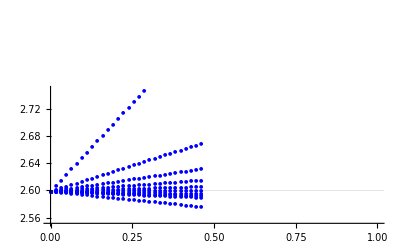

```mathematica
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},Automatic},PlotLegends->Placed["(a)",{0.15,0.85}],PlotMarkers->{Automatic,5},GridLines->{None,{{(1-Ez/wc),{Dashed,Thick,Orange}}}}]
```

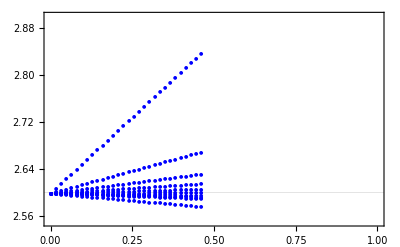

```mathematica
x={2.55,2.9};y=Table[-10+.1*i,{i,0,200}];
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},x},Frame->{True,True,True,True},GridLines->{None,{{(1-Ez/wc),{Dashed,Thickness[0.01],Orange}}}},FrameLabel->{"V_0/π","ω/ω_c",None,None},FrameTicks->{Automatic,y,None,None},PlotMarkers->{Automatic,5}]
```

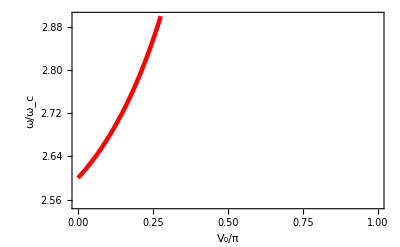

```mathematica
f2=Plot[-(1/wc)*(Ez+Ez*q*(β-α)/(2*(2-(β-α)*q))-Sqrt[Ez^2*((β-α)*q)^2/(4*(2-(β-α)*q)^2)+wc^2*(2-(β-α)*q)/(2-(β+3*α)*q)]),{q,0,1},PlotRange->x,PlotStyle->{Thickness[0.008],Red},Frame->{True,True,True,True},FrameLabel->{"V_0/π","ω/ω_c",None,None},FrameTicks->{Automatic,Automatic,None,None}]
```

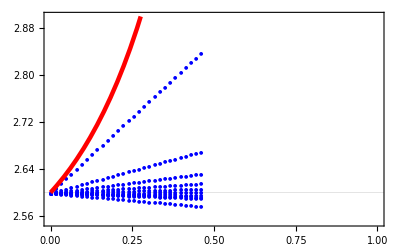

```mathematica
Export["Vp=0_Ez=-1-6wc_nn=9.png",Show[f1,f2,Frame->{True,True,True,True},FrameLabel->{"V_0/π",None,None,None},LabelStyle->Directive[Black,20],FrameTicks->{Automatic,y,None,None}],ImageResolution->600,ImageSize->400];
Show[f1,f2]
```

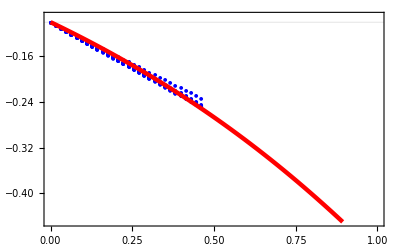

```mathematica
Show[f1,f2]
```

```mathematica
Export[
```

```mathematica
Show[f1,f2]
```

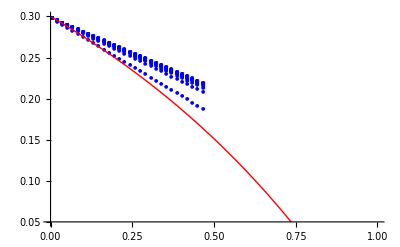

```mathematica
Show[f1,f2]
```

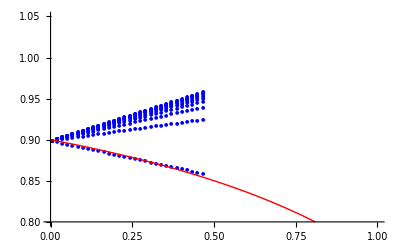

```mathematica
Show[f1,f2]
```

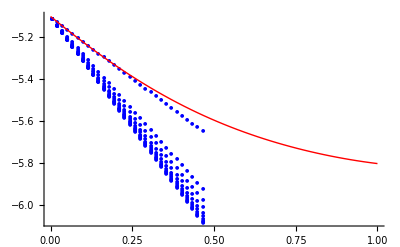

```mathematica
Show[f1,f2]
```

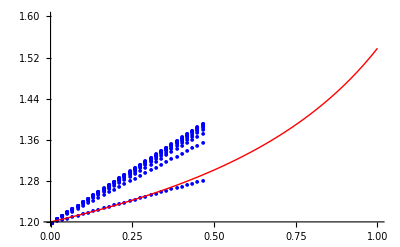

```mathematica
Show[f1,f2]
```

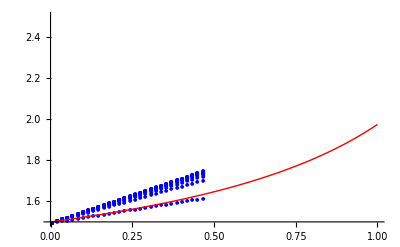

```mathematica
Show[f1,f2]
```

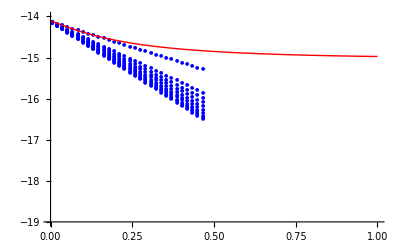

```mathematica
Show[f1,f2]
```

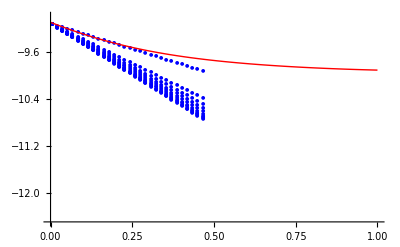

```mathematica
Show[f1,f2]
```

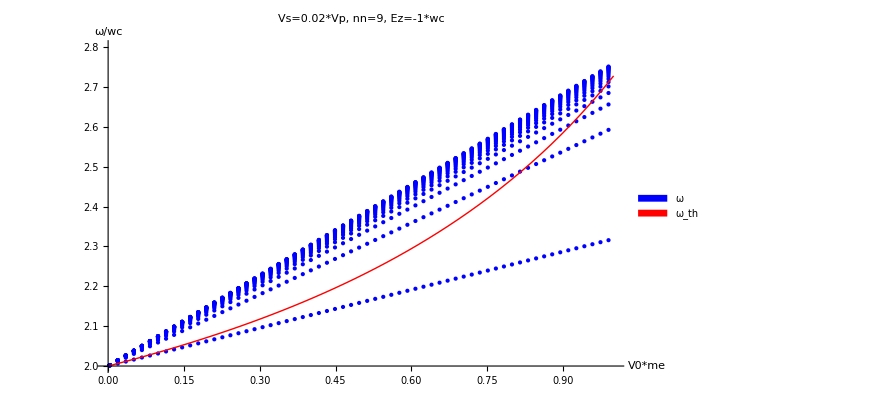

```mathematica
Show[f1,f2]
```

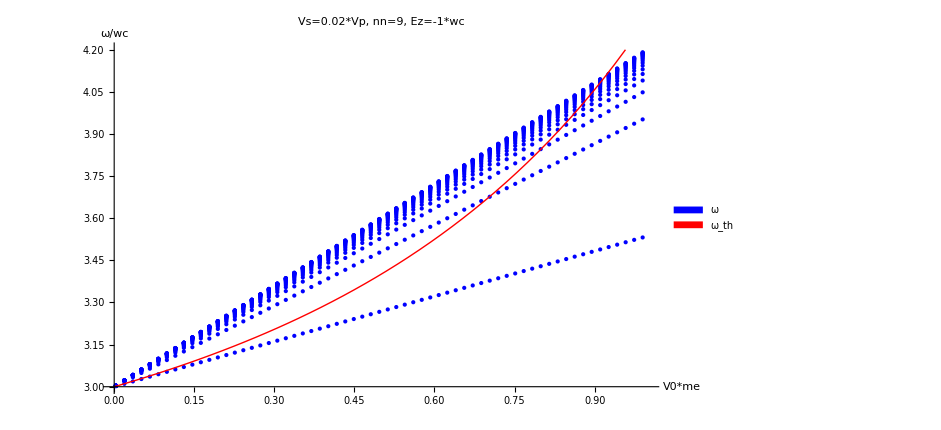

```mathematica
Show[f1,f2]
```

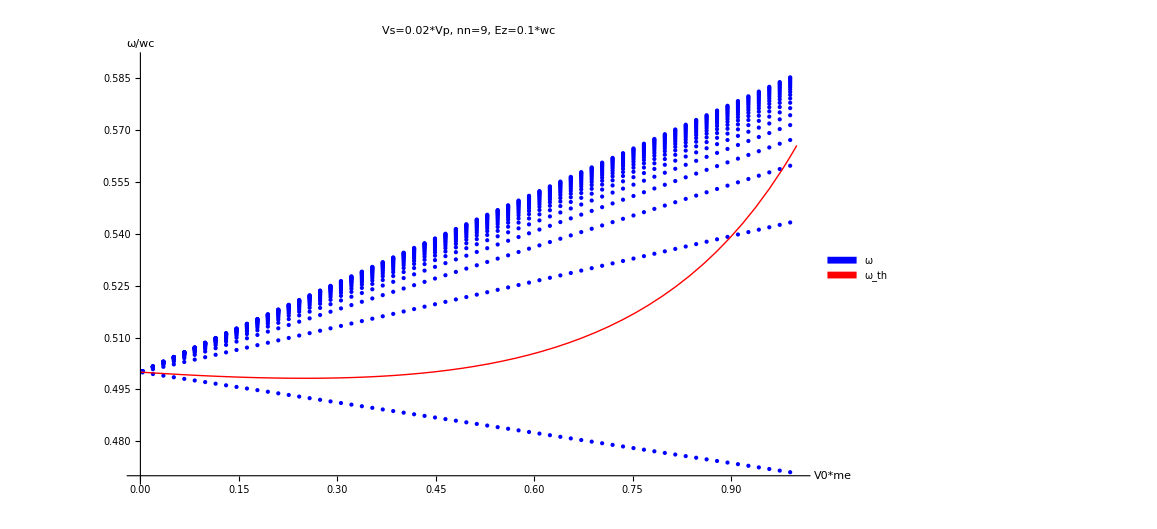

```mathematica
Show[f1,f2]
```

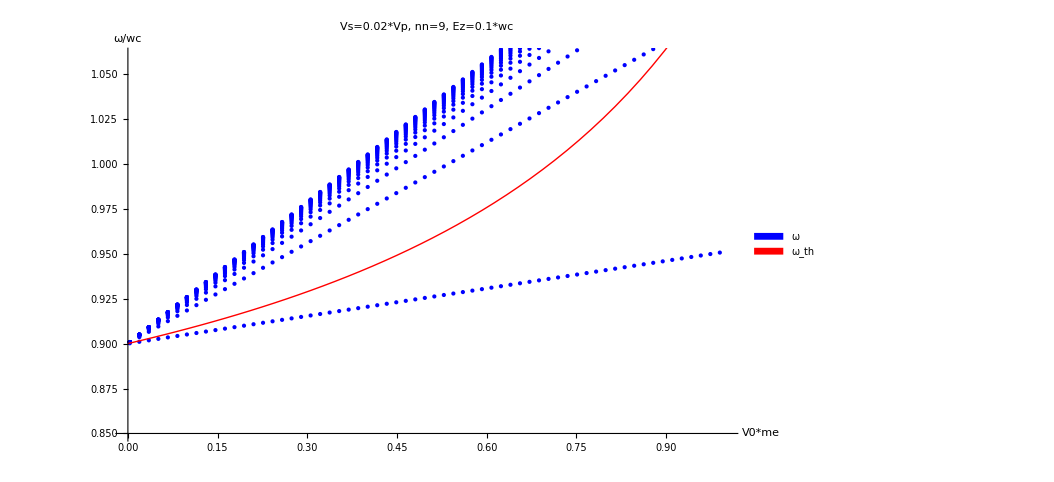

```mathematica
Show[f1,f2]
```

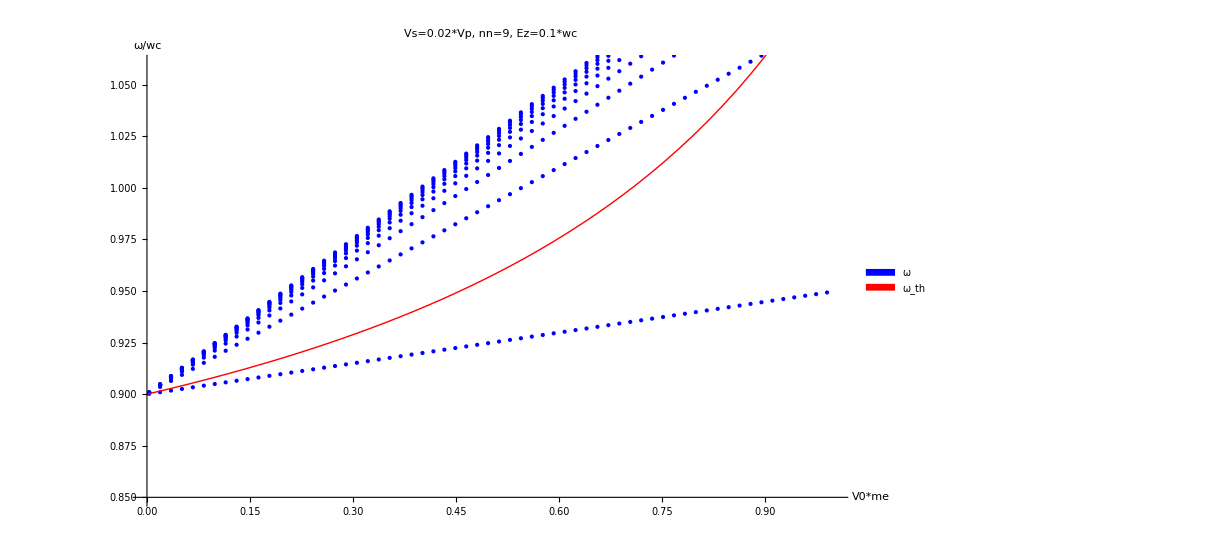

```mathematica
Show[f1,f2]
```

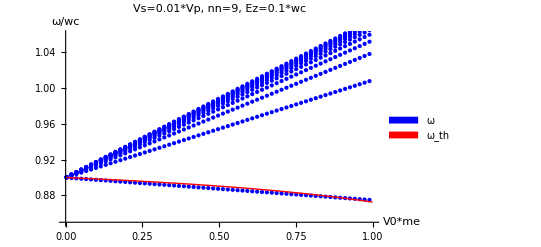

```mathematica
Show[f1,f2]
```

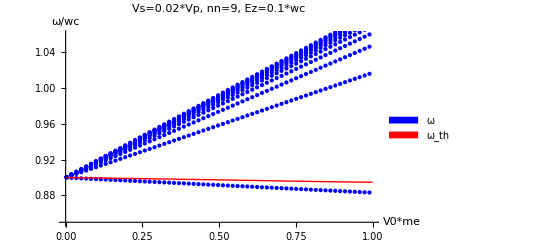

```mathematica
Show[f1,f2]
```